# CEPC Higgs Precision

(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliu2@fnal.gov) for detailed explanation.

## PreCDR

## SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

## CEPC

This is the CEPC fitting program.
For simplicity, I removed many other components involving interfacing with HL-LHC/ILC measurements, other tested fits, etc.

7p and 10p stands for 7-parameter and 10-parameter;
“MD” stands for Model-dependent;
“MI” stands for Model-Independent.

In Prep subsections of both, 
Function_higgsobscepc  defines the processes to be measured at CEPC as a function of model parameters.
Table_higgsprecepc deines the projected precisions on these observables at CEPC.
Function_chisquarecepc defines the χ^2 function used to determine the precisions.

In 7p/10p_Fit_CEPC section, the fitting parameters are defined as in the list of
“arglist”.
As the projected precisions for CEPC measurements are for 5 ab^-1, others are deried by applying luminosity factors in the list “lumi, {xx,...}”, corresponding to luminosity of 5/xx ab^-1.

The results are simply shown in the last matrix in each section.
The rows are corresponding fitting parameters in the “arglsit”;
The columns are different luminosities, currently 0.5, 2, 5, 10 ab^-1;
In each parenthesis, the positive and negative are the allowed interval for the given parameter from their SM expected values.

### 7p_MD_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2,kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0116166
-0.0119323)
(0.016217
-0.0164475)
(0.0146181
-0.0147799)
(0.0119357
-0.0121041)
(0.0132451
-0.0134957)
(0.00153721
-0.00168339)
(0.0456702
-0.0476205))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},%67,%72,%83,%91},8]ᵀ//MatrixForm
```

(kb | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}} | {{0.0116166,-0.0119323}}
kc | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}} | {{0.016217,-0.0164475}}
kg | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}} | {{0.0146182,-0.0147799}}
kw | {{0.0119357,-0.012104}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}} | {{0.0119357,-0.0121041}}
ktau | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}} | {{0.0132451,-0.0134957}}
kz | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}} | {{0.0015372,-0.0016834}}
kgamma | {{0.0456702,-0.0476205}} | {{0.0456702,-0.0476205}} | {{0.04567,-0.0476205}} | {{0.0456702,-0.0476205}})

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | -211647. | -1657.54 | -18420.3 | -67053.8 | -14423.9 | 334803.
-211647. | 80873.4 | 265.739 | 1248.59 | 11081. | 2010.95 | -92077.9
-1657.54 | 265.739 | 989.599 | -18.7214 | 75.1166 | 7.98936 | -1378.92
-18420.3 | 1248.59 | -18.7214 | 53520.4 | -344.352 | -539.374 | -54756.5
-67053.8 | 11081. | 75.1166 | -344.352 | 34524.2 | 445.096 | -48130.7
-14423.9 | 2010.95 | 7.98936 | -539.374 | 445.096 | 16493.5 | -18974.3
334803. | -92077.9 | -1378.92 | -54756.5 | -48130.7 | -18974.3 | 231454.)

```mathematica
Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kz,kw,kgamma,ktau,kg,kt,kb}[[i]],{kz,kw,kgamma,ktau,kg,kt,kb}[[j]]]*If[i==j,1,0]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]
```

(1.42449×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 80873.4 | 0 | 0 | 0 | 0 | 0
0 | 0 | 989.599 | 0 | 0 | 0 | 0
0 | 0 | 0 | 53520.4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 34524.2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 16493.5 | 0
0 | 0 | 0 | 0 | 0 | 0 | 231454.)

```mathematica
Inverse[%39]^0.5.%38.Inverse[%39]^0.5
```

(1. | -0.623564 | -0.0441473 | -0.0667125 | -0.302366 | -0.0941015 | 0.583079
-0.623564 | 1. | 0.0297045 | 0.0189784 | 0.209707 | 0.0550608 | -0.673008
-0.0441473 | 0.0297045 | 1. | -0.00257246 | 0.0128512 | 0.00197754 | -0.0911123
-0.0667125 | 0.0189784 | -0.00257246 | 1. | -0.0080109 | -0.0181541 | -0.491976
-0.302366 | 0.209707 | 0.0128512 | -0.0080109 | 1. | 0.0186525 | -0.538429
-0.0941015 | 0.0550608 | 0.00197754 | -0.0181541 | 0.0186525 | 1. | -0.307099
0.583079 | -0.673008 | -0.0911123 | -0.491976 | -0.538429 | -0.307099 | 1.)

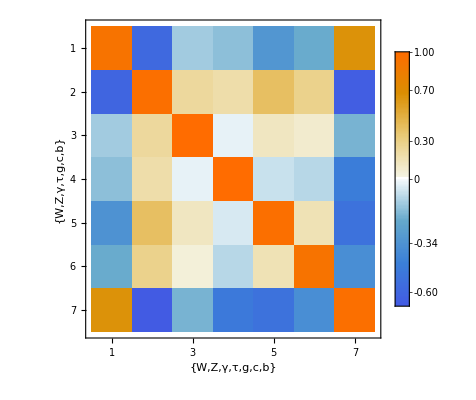

```mathematica
MatrixPlot[%40,FrameLabel->{{"W","Z","γ","τ","g","c","b"},{"W","Z","γ","τ","g","c","b"}},PlotLegends->Automatic]
```

```mathematica
Eigenvalues[%21]
```

{1.45764×10^6,221226.,67099.7,48535.6,30937.8,15919.6,987.163}

### 10p_MI_Fits

#### Prep

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2,kz^2 kb^2/ktotal,kz^2 kt^2/ktotal,kz^2 kg^2/ktotal,kz^2 kw^2/ktotal,kz^2 ktau^2/ktotal,kz^4/ktotal,kz^2 kgamma^2/ktotal,kz^2 kmu^2/ktotal,kw^2 kb^2/ktotal,kz^2brinv+1};
higgsprecepc={0.51/100,0.28/100,2.2/100,1.6/100,1.5/100,1.2/100,4.3/100,9.0/100,17/100,2.8/100,0.14/100};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[(higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)^2/higgsprecepc[[i]]^2/lumif,{i,1,Length[higgsprecepc]}]
```

#### 10p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{10,2.5,1,0.5}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0420525
-0.0403854) | (0.0208194
-0.0204033) | (0.0131192
-0.0129528) | (0.00925944
-0.00917626)
(0.0549682
-0.0530561) | (0.0272377
-0.0267595) | (0.0171701
-0.0169788) | (0.012121
-0.0120254)
(0.0494335
-0.0474334) | (0.0244641
-0.0239643) | (0.015414
-0.0152141) | (0.0108786
-0.0107786)
(0.0387409
-0.0385975) | (0.0193637
-0.0193283) | (0.012244
-0.0122299) | (0.00865667
-0.00864962)
(0.0464184
-0.0444732) | (0.0229652
-0.0224792) | (0.0144679
-0.0142735) | (0.0102101
-0.010113)
(0.00803156
-0.00809659) | (0.00402379
-0.00404005) | (0.00254676
-0.00255326) | (0.0018015
-0.00180475)
(0.14182
-0.157784) | (0.0723428
-0.0762269) | (0.0461336
-0.0476789) | (0.0327644
-0.0335357)
(0.245948
-0.320985) | (0.128651
-0.145883) | (0.082924
-0.0897124) | (0.0592333
-0.0626106)
(0.00442776
-0.00442774) | (0.00221367
-0.00221367) | (0.00140002
-0.00140002) | (0.000989956
-0.000989956)
(0.0910399
-0.0834866) | (0.0445451
-0.0426581) | (0.0279496
-0.0271949) | (0.0196843
-0.019307))

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[(higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

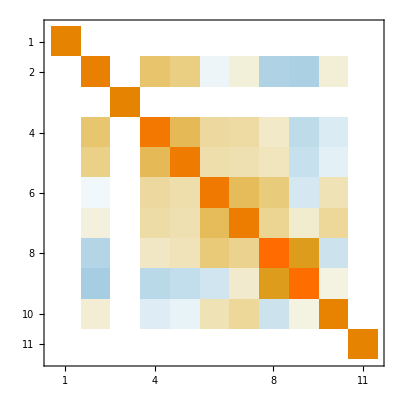

```mathematica
MatrixPlot[inverseinputcorrelations]
```

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0118029
-0.0117799)
(0.0211339
-0.0210743)
(0.0145802
-0.0144704)
(0.013066
-0.0130661)
(0.0133536
-0.0132739)
(0.00124944
-0.00125111)
(0.0361112
-0.0368686))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}}
kc | {{2.11,-2.11}}
kg | {{1.46,-1.45}}
kw | {{1.31,-1.31}}
ktau | {{1.34,-1.33}}
kz | {{0.12,-0.13}}
kgamma | {{3.61,-3.69}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

(160322. | -6920.58 | -25106.6 | -54408.8 | -51941.2 | 136003. | -855.77
-6920.58 | 4057.33 | 2317.66 | 636.328 | -1205.34 | -10368.8 | 3.48455
-25106.6 | 2317.66 | 24988.2 | -788.767 | -4626.86 | -21278.4 | -16.8215
-54408.8 | 636.328 | -788.767 | 50529.1 | -670.021 | -83996.2 | 19.241
-51941.2 | -1205.34 | -4626.86 | -670.021 | 56092.4 | 20726. | -96.6801
136003. | -10368.8 | -21278.4 | -83996.2 | 20726. | 916713. | -1000.06
-855.77 | 3.48455 | -16.8215 | 19.241 | -96.6801 | -1000.06 | 855.506)

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

(1.0002 | 0.634277 | 0.891241 | 0.928746 | 0.947297 | -0.365763 | 0.345717
0.634277 | 0.999881 | 0.493384 | 0.590633 | 0.611401 | -0.138108 | 0.221453
0.891241 | 0.493384 | 1.00011 | 0.84096 | 0.858591 | -0.27462 | 0.312383
0.928746 | 0.590633 | 0.84096 | 1.0002 | 0.877789 | -0.203175 | 0.325402
0.947297 | 0.611401 | 0.858591 | 0.877789 | 1.00015 | -0.366908 | 0.33096
-0.365763 | -0.138108 | -0.27462 | -0.203175 | -0.366908 | 1. | -0.0934936
0.345717 | 0.221453 | 0.312383 | 0.325402 | 0.33096 | -0.0934936 | 0.998827)

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.634252 | 0.891103 | 0.928563 | 0.947136 | -0.365727 | 0.345886
0.634252 | 1. | 0.493385 | 0.590609 | 0.611392 | -0.138116 | 0.221596
0.891103 | 0.493385 | 1. | 0.840829 | 0.85848 | -0.274604 | 0.312548
0.928563 | 0.590609 | 0.840829 | 1. | 0.877638 | -0.203155 | 0.32556
0.947136 | 0.611392 | 0.85848 | 0.877638 | 1. | -0.366881 | 0.33113
-0.365727 | -0.138116 | -0.274604 | -0.203155 | -0.366881 | 1. | -0.0935484
0.345886 | 0.221596 | 0.312548 | 0.32556 | 0.33113 | -0.0935484 | 1.)

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},Abs[cepc7p]*100,Abs[cepc7pL]*100},2]ᵀ//MatrixForm
```

(kb | {{1.2,1.2}} | {{0.9,0.9}}
kc | {{2.1,2.1}} | {{1.9,1.9}}
kg | {{1.5,1.4}} | {{1.1,1.1}}
kw | {{1.3,1.3}} | {{1.,1.}}
ktau | {{1.3,1.3}} | {{1.1,1.1}}
kz | {{0.1,0.1}} | {{0.1,0.1}}
kgamma | {{3.6,3.7}} | {{1.6,1.6}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.92,-0.92}}
kc | {{1.86,-1.86}}
kg | {{1.12,-1.11}}
kw | {{1.02,-1.02}}
ktau | {{1.06,-1.06}}
kz | {{0.12,-0.12}}
kgamma | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{163850.,-6765.56,-30395.9,-53159.4,-51571.5,130191.,-842.466},{-6765.56,4464.51,1672.6,694.216,-1188.21,-10629.7,4.10095},{-30395.9,1672.6,34243.3,-2763.87,-5211.36,-12872.4,-37.8527},{-53159.4,694.216,-2763.87,53263.2,-531.952,-88366.1,24.209},{-51571.5,-1188.21,-5211.36,-531.952,56566.4,19670.8,-95.21},{130191.,-10629.7,-12872.4,-88366.1,19670.8,932650.,-4108.87},{-842.466,4.10095,-37.8527,24.209,-95.21,-4108.87,3941.98}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00007 | 0.568505 | 0.869307 | 0.884889 | 0.916009 | -0.305686 | 0.11436
0.568505 | 0.99986 | 0.446228 | 0.506599 | 0.536605 | -0.0609252 | 0.0729729
0.869307 | 0.446228 | 1.00004 | 0.791765 | 0.816929 | -0.228556 | 0.104253
0.884889 | 0.506599 | 0.791765 | 1.00007 | 0.807764 | -0.0926284 | 0.114409
0.916009 | 0.536605 | 0.816929 | 0.807764 | 1.00004 | -0.306455 | 0.105363
-0.305686 | -0.0609252 | -0.228556 | -0.0926284 | -0.306455 | 1. | 0.0352107
0.11436 | 0.0729729 | 0.104253 | 0.114409 | 0.105363 | 0.0352107 | 0.999981)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.568526 | 0.86926 | 0.884826 | 0.915959 | -0.305676 | 0.114357
0.568526 | 1. | 0.44625 | 0.506615 | 0.536632 | -0.0609295 | 0.0729788
0.86926 | 0.44625 | 1. | 0.791719 | 0.816895 | -0.228551 | 0.104252
0.884826 | 0.506615 | 0.791719 | 1. | 0.807718 | -0.0926249 | 0.114405
0.915959 | 0.536632 | 0.816895 | 0.807718 | 1. | -0.306449 | 0.105362
-0.305676 | -0.0609295 | -0.228551 | -0.0926249 | -0.306449 | 1. | 0.035211
0.114357 | 0.0729788 | 0.104252 | 0.114405 | 0.105362 | 0.035211 | 1.)

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0129954
-0.0129244)
(0.0216494
-0.0215376)
(0.0155011
-0.0153488)
(0.0138088
-0.0137778)
(0.0145525
-0.0144235)
(0.00249677
-0.0025029)
(0.0364716
-0.0371533)
(0.0834764
-0.0903147)
(0.00150002
-0.00150001)
(0.0287935
-0.0281479))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}}
kt | {{2.16,-2.15}}
kg | {{1.55,-1.53}}
kw | {{1.38,-1.38}}
ktau | {{1.46,-1.44}}
kz | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}}
kmu | {{8.35,-9.03}}
brinv | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00017 | 0.651845 | 0.90324 | 0.933432 | 0.955589 | 0.192915 | 0.366548 | 0.155284 | 0. | 0.981764
0.651845 | 0.999876 | 0.525309 | 0.614638 | 0.632549 | 0.115783 | 0.242468 | 0.102719 | 0. | 0.64735
0.90324 | 0.525309 | 1.0001 | 0.857997 | 0.87563 | 0.162086 | 0.335992 | 0.142339 | 0. | 0.897333
0.933432 | 0.614638 | 0.857997 | 1.0002 | 0.89039 | 0.181259 | 0.347828 | 0.147354 | 0. | 0.931309
0.955589 | 0.632549 | 0.87563 | 0.89039 | 1.00012 | 0.172568 | 0.353482 | 0.149749 | 0. | 0.944404
0.192915 | 0.115783 | 0.162086 | 0.181259 | 0.172568 | 1.00013 | 0.0679164 | 0.0287721 | 0. | 0.351261
0.366548 | 0.242468 | 0.335992 | 0.347828 | 0.353482 | 0.0679164 | 0.998814 | 0.0574918 | 0. | 0.362868
0.155284 | 0.102719 | 0.142339 | 0.147354 | 0.149749 | 0.0287721 | 0.0574918 | 0.992493 | 0. | 0.153725
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999976 | 0.
0.981764 | 0.64735 | 0.897333 | 0.931309 | 0.944404 | 0.351261 | 0.362868 | 0.153725 | 0. | 1.00006)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.651831 | 0.903117 | 0.933261 | 0.955451 | 0.192886 | 0.366734 | 0.155857 | 0. | 0.981654
0.651831 | 1. | 0.525314 | 0.614615 | 0.63255 | 0.115783 | 0.242627 | 0.103113 | 0. | 0.647372
0.903117 | 0.525314 | 1. | 0.857867 | 0.875532 | 0.162067 | 0.336173 | 0.142869 | 0. | 0.897261
0.933261 | 0.614615 | 0.857867 | 1. | 0.890247 | 0.181229 | 0.348 | 0.147895 | 0. | 0.93119
0.955451 | 0.63255 | 0.875532 | 0.890247 | 1. | 0.172546 | 0.353671 | 0.150305 | 0. | 0.94432
0.192886 | 0.115783 | 0.162067 | 0.181229 | 0.172546 | 1. | 0.0679522 | 0.0288788 | 0. | 0.351228
0.366734 | 0.242627 | 0.336173 | 0.348 | 0.353671 | 0.0679522 | 1. | 0.057743 | 0. | 0.363073
0.155857 | 0.103113 | 0.142869 | 0.147895 | 0.150305 | 0.0288788 | 0.057743 | 1. | 0. | 0.154301
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.981654 | 0.647372 | 0.897261 | 0.93119 | 0.94432 | 0.351228 | 0.363073 | 0.154301 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.0103186
-0.0102576)
(0.0190288
-0.0189831)
(0.0120981
-0.0119974)
(0.0108282
-0.0107985)
(0.0117734
-0.0116744)
(0.00249688
-0.00250313)
(0.0162701
-0.0162915)
(0.0494669
-0.0502318)
(0.00150001
-0.00150002)
(0.0233043
-0.0228486))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}} | {{1.03,-1.03}}
kt | {{2.16,-2.15}} | {{1.9,-1.9}}
kg | {{1.55,-1.53}} | {{1.21,-1.2}}
kw | {{1.38,-1.38}} | {{1.08,-1.08}}
ktau | {{1.46,-1.44}} | {{1.18,-1.17}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}} | {{1.63,-1.63}}
kmu | {{8.35,-9.03}} | {{4.95,-5.02}}
brinv | {{0.15,-0.15}} | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}} | {{2.33,-2.28}})

```mathematica
-Graphics-;
```

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 1.3 | 1.
kt | 2.2 | 1.9
kg | 1.5 | 1.2
kw | 1.4 | 1.1
ktau | 1.4 | 1.2
kz | 0.2 | 0.3
kgamma | 3.7 | 1.6
kmu | 8.7 | 5.
brinv | 0.2 | 0.2
ktotal | 2.8 | 2.3)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.014488,0.00249984,0.0368124,0.0868956,0.00150002,0.0284707}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00004 | 0.587306 | 0.888449 | 0.89504 | 0.931422 | 0.242999 | 0.170569 | 0.079863 | 0. | 0.972108
0.587306 | 0.999853 | 0.480479 | 0.534928 | 0.561192 | 0.131537 | 0.100895 | 0.0475803 | 0. | 0.581922
0.888449 | 0.480479 | 1.00002 | 0.817183 | 0.844922 | 0.207507 | 0.153268 | 0.072064 | 0. | 0.879634
0.89504 | 0.534928 | 0.817183 | 1.00007 | 0.831244 | 0.231195 | 0.157685 | 0.0736481 | 0. | 0.894973
0.931422 | 0.561192 | 0.844922 | 0.831244 | 1.00002 | 0.213239 | 0.159251 | 0.0749429 | 0. | 0.915309
0.242999 | 0.131537 | 0.207507 | 0.231195 | 0.213239 | 0.999994 | 0.153555 | 0.050151 | 0. | 0.43334
0.170569 | 0.100895 | 0.153268 | 0.157685 | 0.159251 | 0.153555 | 0.999969 | 0.0174489 | 0. | 0.191394
0.079863 | 0.0475803 | 0.072064 | 0.0736481 | 0.0749429 | 0.050151 | 0.0174489 | 0.999778 | 0. | 0.0851411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999979 | 0.
0.972108 | 0.581922 | 0.879634 | 0.894973 | 0.915309 | 0.43334 | 0.191394 | 0.0851411 | 0. | 0.999929)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00002,0.999926,1.00001,1.00004,1.00001,0.999997,0.999985,0.999889,0.99999,0.999964}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

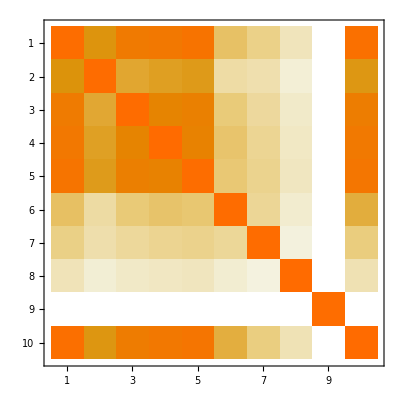

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## CDR (width subchannel ZZ)

```mathematica
higgsprecepcoriginal=higgsprecepc
```

{0.171,0.0082,0.0684,0.0098,0.0509,0.0127,0.0326,0.003068,0.029991,∞,0.005}

```mathematica
higgsprecepc=Table[If[i==5||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,∞,0.0509,∞,∞,∞,∞,∞,0.005}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={Infinity,Infinity,Infinity,Infinity,5.07,Infinity,Infinity,Infinity,Infinity,Infinity,0.5}/100;
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+40000. (-1+kz^2)^2+389.031 (-1+kz^4/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[%,kz][[1]]},{x,0,0.1,0.002}]
```

{{0.,0.},{0.002,0.0014921},{0.004,0.00594552},{0.006,0.0133262},{0.008,0.0236006},{0.01,0.0367353},{0.012,0.0526976},{0.014,0.0714548},{0.016,0.0929748},{0.018,0.117226},{0.02,0.144177},{0.022,0.173796},{0.024,0.206053},{0.026,0.240918},{0.028,0.278359},{0.03,0.318349},{0.032,0.360857},{0.034,0.405854},{0.036,0.453312},{0.038,0.503202},{0.04,0.555495},{0.042,0.610166},{0.044,0.667185},{0.046,0.726525},{0.048,0.788161},{0.05,0.852064},{0.052,0.91821},{0.054,0.986572},{0.056,1.05712},{0.058,1.12984},{0.06,1.2047},{0.062,1.28167},{0.064,1.36073},{0.066,1.44186},{0.068,1.52503},{0.07,1.61022},{0.072,1.6974},{0.074,1.78655},{0.076,1.87766},{0.078,1.97068},{0.08,2.06562},{0.082,2.16243},{0.084,2.2611},{0.086,2.36161},{0.088,2.46393},{0.09,2.56805},{0.092,2.67394},{0.094,2.78159},{0.096,2.89096},{0.098,3.00205},{0.1,3.11483}}

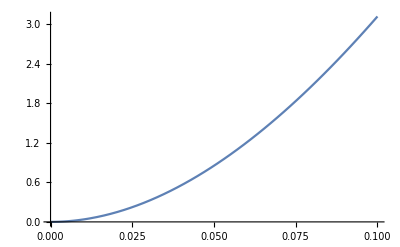

{{x→0.0543855}}

```mathematica
Plot[Interpolation[tempdata][x],{x,0,0.1}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

## CDR (width subchannel WW)

```mathematica
higgsprecepc=Table[If[i==4||i==8||i==9||i==11,higgsprecepcoriginal[[i]],Infinity],{i,1,11}]
```

{∞,∞,∞,0.0098,∞,∞,∞,0.003068,0.029991,∞,0.005}

```mathematica
higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inputcorrelations[[i,j]]/100/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
```

```mathematica
func=chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,0,ktotal},1]
```

0.+1111.78 (-1+(kb^2 kw^2)/ktotal)^2+40000. (-1+kz^2)^2-10478.4 (-1+(kb^2 kw^2)/ktotal) (-1+(kb^2 kz^2)/ktotal)+106240. (-1+(kb^2 kz^2)/ktotal)^2-31.8463 (-1+(kb^2 kw^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+645.239 (-1+(kb^2 kz^2)/ktotal) (-1+(kw^2 kz^2)/ktotal)+10412.3 (-1+(kw^2 kz^2)/ktotal)^2

```mathematica
func/.ktotal->1+x;
tempdata=Table[{x,NMinimize[{%,0<kz<2,0<kw<2,0<kb<2},{kz,kw,kb}][[1]]},{x,-0.1,0.1,0.002}]
```

{{-0.1,8.0851},{-0.098,7.76173},{-0.096,7.44509},{-0.094,7.13516},{-0.092,6.83194},{-0.09,6.53541},{-0.088,6.24558},{-0.086,5.96243},{-0.084,5.68595},{-0.082,5.41615},{-0.08,5.153},{-0.078,4.89652},{-0.076,4.64667},{-0.074,4.40347},{-0.072,4.16689},{-0.07,3.93694},{-0.068,3.71361},{-0.066,3.49689},{-0.064,3.28676},{-0.062,3.08323},{-0.06,2.88628},{-0.058,2.69591},{-0.056,2.51211},{-0.054,2.33487},{-0.052,2.16419},{-0.05,2.00004},{-0.048,1.84244},{-0.046,1.69137},{-0.044,1.54682},{-0.042,1.40878},{-0.04,1.27724},{-0.038,1.15221},{-0.036,1.03366},{-0.034,0.921593},{-0.032,0.816},{-0.03,0.716871},{-0.028,0.624198},{-0.026,0.537973},{-0.024,0.458188},{-0.022,0.384834},{-0.02,0.317903},{-0.018,0.257386},{-0.016,0.203276},{-0.014,0.155563},{-0.012,0.11424},{-0.01,0.0792977},{-0.008,0.0507277},{-0.006,0.0285214},{-0.004,0.0126705},{-0.002,0.00316618},{0.,1.63667×10^-21},{0.002,0.00316331},{0.004,0.0126475},{0.006,0.0284438},{0.008,0.0505437},{0.01,0.0789384},{0.012,0.113619},{0.014,0.154577},{0.016,0.201804},{0.018,0.25529},{0.02,0.315028},{0.022,0.381008},{0.024,0.453221},{0.026,0.531658},{0.028,0.616311},{0.03,0.707171},{0.032,0.804228},{0.034,0.907474},{0.036,1.0169},{0.038,1.1325},{0.04,1.25426},{0.042,1.38217},{0.044,1.51622},{0.046,1.65641},{0.048,1.80273},{0.05,1.95516},{0.052,2.1137},{0.054,2.27834},{0.056,2.44907},{0.058,2.62588},{0.06,2.80876},{0.062,2.9977},{0.064,3.19269},{0.066,3.39373},{0.068,3.6008},{0.07,3.81389},{0.072,4.03301},{0.074,4.25812},{0.076,4.48924},{0.078,4.72634},{0.08,4.96942},{0.082,5.21848},{0.084,5.47349},{0.086,5.73445},{0.088,6.00135},{0.09,6.27418},{0.092,6.55294},{0.094,6.83761},{0.096,7.12818},{0.098,7.42465},{0.1,7.72701}}

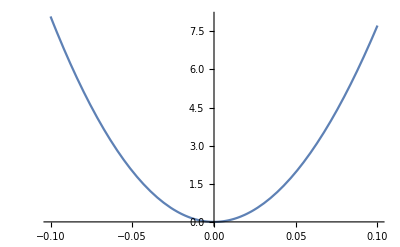

{{x→0.0356983}}

```mathematica
Plot[Interpolation[tempdata][x],{x,-0.1,0.1}]
NSolve[Interpolation[tempdata][x]==1,x]//Quiet
```

# MuC Higgs Precision

(Dated: Sep. 11th,2015)
(Updated: Sep. 2017 for CEPC CDR）
(Updated: Oct. 2017 for CEPC CDR, with covariance matrix)
This code is used to determine projected Higgs precision achievable at Circular-Elector-Positron-Collider. 

A proper definition of projected precision has many physical requirements and can be defined in several different ways. The definition of precision on each parameter is using profiled-likelihood. Technically the definition is as follows, 
a) define a likelihood function;
a.a) here we take the probability P as -2Log[P]=χ^2 up to proper normalization;
a.b) χ^2 is defined as sum of (obs.-exp.)^2/(σ^2)_(Obs.), where obs. and exp. stands for observed and expected quantity and σ stands for the standard deviation;
b) find the allowed 1-sigma regions for a (set of) given parameter(s) κ(s);
b.a) this is equivalent to finding the largest range of  κ(s) that follow Δχ^2=χ^2-χ_min^2≤1;
b.b) “profiled” means while attempting to find such range, all the other parameters are allowed to vary freely within physical boundaries to minimize Δχ^2.
This program uses very simple linear regression method in finding such intervals. The efficiency of such algorithm decreases drastically for constrained fits with complex boundary conditions.

This fitting provides us guidance in prioritizing channels to study for the purpose of precision Higgs physics. Such guidance is indirect, only reveals itself via studying. 

Please consult Zhen Liu (zliu2@fnal.gov) for detailed explanation.

## CDR

### SM input

Branching ratios of the SM Higgs, 
assuming 125 GeV and reading from LHC Higgs cross section work group (cern twiki page).

```mathematica
brb=0.578;brtau=0.0637;brmu=2.21 10^-4;brs=4.4 10^-4;brc=2.68 10^-2;brg=8.56 10^-2;brgamma=2.30 10^-3;brw=0.216;brz=0.0267;
```

Higgs total width definition, only used when doing constrained fits where Higgs width is a derived quantity from other fitting parameters.

```mathematica
kh[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:=kb^2 brb+kw^2 brw+kz^2 brz+ktau^2 brtau+kg^2 brg+kgamma^2 brgamma+kt^2 brc+kb^2 brs+ktau^2 brmu+(1-brb-brw-brz-brtau-brg-brgamma-brc-brs-brmu);
```

Note: above branching fractions do not sum up to be exactly one, its up to the user to add the last piece

```mathematica
kh[1,1,1,1,1,1,1]
```

1.

### Prep (input)

```mathematica
(*higgsobscepc[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^4/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],6/7 kz^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau]+1/7 kw^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kz^2};
higgsprecepc={(0.149731+0.158474)*100/2,(0.0133717+0.0133935)*100/2,(0.0807207+0.0820905)*100/2,(0.0126807+0.0128432)*100/2,(0.049666+0.0509421)*100/2,(0.0144769+0.0144958)*100/2,(0.0352087+0.035472)*100/2,(0.00326826+0.00326885)*100/2,(0.0311003+0.0312155)*100/2,(0.00472532+0.00472881)*100/2,(0.00498383+0.00500063)*100/2}/100;
higgsprecepc={15.9,0.888,8.32,1.03,5.07,1.42,3.55,(0.00326191+0.00326551)*100/2,(0.0311003+0.0312155)*100/2,Infinity(*(0.00401209+0.00402172)*100/2*),0.5}/100;
inputcorrelations=(*Nov.6.2017*){{100,-0.475,-0.086,-0.365,-0.164,-0.046,0.018,-0.002,0.004,0},{-0.475,100,-1.115,-5.857,-2.343,0.454,0.133,0.005,-0.011,0},{-0.086,-1.115,100,-0.918,-0.398,0.093,0.017,-0.005,0.011,0},{-0.365,-5.857,-0.918,100,-6.530,-8.025,-5.704,-0.031,0.074,0},{-0.164,-2.343,-0.398,-6.530,100,-1.793,-1.380,0.588,-1.379,0},{-0.046,0.454,0.093,-8.025,-1.793,100,-15.768,-0.290,0.679,0},{0.018,0.133,0.017,-5.704,-1.380,-15.768,100,4.446,-10.425,0},{-0.002,0.005,-0.005,-0.031,0.588,-0.290,4.446,100,-42.653,0},{0.004,-0.011,0.011,0.074,-1.379,0.679,-10.425,-42.653,100,0},{0,0,0,0,0,0,0,0,0,100}};
inputcorrelations=(*Jan.7.2018*){{100,-2.58,-0.29,-0.58,-0.16,0.40,-0.68,0.14,-0.06,0.09,0},{-2.58,100,-6.14,-18.57,-6.47,9.50,-5.36,3.45,-1.58,-0.51,0},{-0.29,-6.14,100,0.33,-0.38,0.08,-0.63,0.06,-0.03,0.14,0},{-0.58,-18.57,0.33,100,-16.34,-33.83,-13.56,-8.42,3.87,1.10,0},{-0.16,-6.47,-0.38,-16.34,100,-10.85,-6.65,-11.85,5.44,-4.15,0},{0.40,9.50,0.08,-33.83,-10.85,100,-16.72,-6.77,3.11,-1.05,0},{-0.68,-5.36,-0.63,-13.56,-6.65,-16.72,100,-4.13,1.90,-6.20,0},{0.14,3.45,0.06,-8.42,-11.85,-6.77,-4.13,100,-45.91,1.35,0},
{-0.06,-1.58,-0.03,3.87,5.44,3.11,1.90,-45.91,100,-0.62,0},{0.09,-0.51,0.14,1.10,-4.15,-1.05,-6.20,1.35,-0.62,100,0},{0,0,0,0,0,0,0,0,0,0,100}};
halfcorrelation=(*Apr.15.2018*)SparseArray[{{11,11}->0,{4,2}->-22.661,{5,2}->-14.181,{6,2}->9.214,{7,2}->2.329,{8,2}->4.237,{9,2}->-1.974,{10,2}->0.257,{5,4}->-12.487,{6,4}->-27.633,{7,4}->-10.609,{8,4}->-7.886,{9,4}->3.675,{10,4}->1.658,{6,5}->-13.483,{7,5}->-6.800,{8,5}->-12.420,{9,5}->5.788,{10,5}->-4.351,{7,6}->-19.209,{8,6}->-7.648,{9,6}-> 3.564,{10,6}->-1.081,{8,7}-> -4.463,{9,7}-> 2.080,{10,7}-> -6.389,{9,8}-> -46.606,{10,8}-> 1.335,{10,9}-> -0.622}]//Normal;
inputcorrelations=(*Apr.15.2018*)IdentityMatrix[11]*100+halfcorrelationᵀ+halfcorrelation;
(*chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[If[i==j,((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])/lumif,0],{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]*)*)
```

### Defining χ^2 s

```mathematica
(*Following Frederick James P.68-69 for defintions of correlation matrix, covariance matrix, etc.*)
(*inverseinputcorrelations is actually the precision/conentration matrix*)
```

```mathematica
Inverse[{{1,ρ},{ρ,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2)
-ρ/(1-ρ^2) | 1/(1-ρ^2))

```mathematica
Inverse[{{1,ρ,0},{ρ,1,0},{0,0,1}}]//MatrixForm
```

(1/(1-ρ^2) | -ρ/(1-ρ^2) | 0
-ρ/(1-ρ^2) | 1/(1-ρ^2) | 0
0 | 0 | 1)

```mathematica
inverseinputcorrelations=Inverse[inputcorrelations/100];
%//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
chisquarecepc[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
(*higgspreLHCratiosH={5.7/100,2.6/100,3.1/100,9.8/100,8.9/100,8.7/100,8/100,9.4/100,6.3/100};*)
chisquarecepcL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+Sum[(higgsobsLHCratios[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
higgsobscepc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,brinv_,ktotal_]:={kz^2 kmu^2/ktotal,kz^2 ktau^2/ktotal,kz^2 kgamma^2/ktotal,kz^2 kw^2/ktotal,kz^4/ktotal,kz^2 kg^2/ktotal,kz^2 kt^2/ktotal,kz^2 kb^2/ktotal,kw^2 kb^2/ktotal,6/7 kz^2 kb^2/ktotal+1/7 kw^2 kb^2/ktotal,kz^2,kz^2brinv+1};
chisquarecepc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2
higgsobsLHCratios10p[kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_]:={kg^2 kz^2/ktotal,kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,kmu/kz};
chisquarecepc10pL[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,brinv_,ktotal_},lumif_]:=Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/lumif,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]+(higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, brinv, ktotal][[-1]]-1)^2/higgsobscepcinv^2+Sum[(higgsobsLHCratios10p[kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal][[i]]-1)^2/higgspreLHCratiosL[[i]]^2,{i,1,Length[higgspreLHCratiosL]}]
```

```mathematica
MatrixPlot[inverseinputcorrelations]
```

-Graphics-

```mathematica
inverseinputcorrelations//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.03799 | 0. | 0.186831 | 0.127052 | -7.97643×10^-7 | 2.54771×10^-6 | -0.000266311 | -0.000551517 | 2.77031×10^-6 | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.186831 | 0. | 1.10228 | 0.286426 | 0.0613319 | 0.0541955 | 0.00631621 | -0.0000949759 | -2.2074×10^-6 | 0.
0. | 0.127052 | 0. | 0.286426 | 1.08205 | 0.0450032 | 0.0346638 | 0.0285587 | -0.0000708832 | -9.55433×10^-7 | 0.
0. | -7.97643×10^-7 | 0. | 0.0613319 | 0.0450032 | 1.08837 | 0.271105 | 0.156356 | -2.41688×10^-6 | 0.0311889 | 0.
0. | 2.54771×10^-6 | 0. | 0.0541955 | 0.0346638 | 0.271105 | 1.07599 | 0.0941278 | 3.18245×10^-6 | 0.0694544 | 0.
0. | -0.000266311 | 0. | 0.00631621 | 0.0285587 | 0.156356 | 0.0941278 | 1.32879 | 0.628015 | -4.00611×10^-6 | 0.
0. | -0.000551517 | 0. | -0.0000949759 | -0.0000708832 | -2.41688×10^-6 | 3.18245×10^-6 | 0.628015 | 1.30275 | 8.9589×10^-7 | 0.
0. | 2.77031×10^-6 | 0. | -2.2074×10^-6 | -9.55433×10^-7 | 0.0311889 | 0.0694544 | -4.00611×10^-6 | 8.9589×10^-7 | 1.00475 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
inputcorrelations-inputcorrelationsᵀ//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0. | 0 | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0 | 0. | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0 | 0. | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0 | 0. | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0 | 0. | 0
0 | 0. | 0 | 0. | 0. | 0. | 0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 7p_fit_CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepc[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepc[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
cepc7p//MatrixForm
```

((0.0118029
-0.0117799)
(0.0211339
-0.0210743)
(0.0145802
-0.0144704)
(0.013066
-0.0130661)
(0.0133536
-0.0132739)
(0.00124944
-0.00125111)
(0.0361112
-0.0368686))

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}}
kc | {{2.11,-2.11}}
kg | {{1.46,-1.45}}
kw | {{1.31,-1.31}}
ktau | {{1.34,-1.33}}
kz | {{0.12,-0.13}}
kgamma | {{3.61,-3.69}})

```mathematica
concentrationmatrix7p=Table[D[chisquarecepc[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2;
%//MatrixForm
```

(160322. | -6920.58 | -25106.6 | -54408.8 | -51941.2 | 136003. | -855.77
-6920.58 | 4057.33 | 2317.66 | 636.328 | -1205.34 | -10368.8 | 3.48455
-25106.6 | 2317.66 | 24988.2 | -788.767 | -4626.86 | -21278.4 | -16.8215
-54408.8 | 636.328 | -788.767 | 50529.1 | -670.021 | -83996.2 | 19.241
-51941.2 | -1205.34 | -4626.86 | -670.021 | 56092.4 | 20726. | -96.6801
136003. | -10368.8 | -21278.4 | -83996.2 | 20726. | 916713. | -1000.06
-855.77 | 3.48455 | -16.8215 | 19.241 | -96.6801 | -1000.06 | 855.506)

```mathematica
covariancematrix7p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7].concentrationmatrix7p.(((#[[1,1]]-#[[1,2]])/2&/@cepc7p) IdentityMatrix[7])];
%//MatrixForm
```

(1.0002 | 0.634277 | 0.891242 | 0.928747 | 0.947297 | -0.365763 | 0.345718
0.634277 | 0.99988 | 0.493384 | 0.590633 | 0.6114 | -0.138108 | 0.221453
0.891242 | 0.493384 | 1.00011 | 0.84096 | 0.858591 | -0.274619 | 0.312383
0.928747 | 0.590633 | 0.84096 | 1.0002 | 0.877788 | -0.203175 | 0.325402
0.947297 | 0.6114 | 0.858591 | 0.877788 | 1.00014 | -0.366908 | 0.33096
-0.365763 | -0.138108 | -0.274619 | -0.203175 | -0.366908 | 1. | -0.0934935
0.345718 | 0.221453 | 0.312383 | 0.325402 | 0.33096 | -0.0934935 | 0.998828)

```mathematica
correlationmatrix7p=Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]].covariancematrix7p.Inverse[Sqrt[Diagonal[covariancematrix7p]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.634252 | 0.891103 | 0.928563 | 0.947136 | -0.365727 | 0.345886
0.634252 | 1. | 0.493385 | 0.590609 | 0.611392 | -0.138116 | 0.221596
0.891103 | 0.493385 | 1. | 0.840829 | 0.85848 | -0.274604 | 0.312548
0.928563 | 0.590609 | 0.840829 | 1. | 0.877638 | -0.203155 | 0.32556
0.947136 | 0.611392 | 0.85848 | 0.877638 | 1. | -0.366881 | 0.33113
-0.365727 | -0.138116 | -0.274604 | -0.203155 | -0.366881 | 1. | -0.0935484
0.345886 | 0.221596 | 0.312548 | 0.32556 | 0.33113 | -0.0935484 | 1.)

### 7p_fit_CEPC_LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
cepc7pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistp[[i]]];{chisquarecepcL[inputlist,lumif],kg> 0,kg<2,kgamma>0,kgamma<2,kb> 0,kb<2,kt> 0,kt<2,ktau> 0,ktau<2, kz<2, kz>0, kw<2, kw>0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[inputlist=ReplacePart[arglist,i->1+dlistm[[i]]];{chisquarecepcL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0},{kz,kg,kgamma,kw,kb,kt,ktau}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
```

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7p*100,cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.18,-1.18}} | {{0.92,-0.92}}
kc | {{2.11,-2.11}} | {{1.86,-1.86}}
kg | {{1.46,-1.45}} | {{1.12,-1.11}}
kw | {{1.31,-1.31}} | {{1.02,-1.02}}
ktau | {{1.34,-1.33}} | {{1.06,-1.06}}
kz | {{0.12,-0.13}} | {{0.12,-0.12}}
kgamma | {{3.61,-3.69}} | {{1.61,-1.61}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},Abs[cepc7p]*100,Abs[cepc7pL]*100},2]ᵀ//MatrixForm
```

(kb | {{1.2,1.2}} | {{0.9,0.9}}
kc | {{2.1,2.1}} | {{1.9,1.9}}
kg | {{1.5,1.4}} | {{1.1,1.1}}
kw | {{1.3,1.3}} | {{1.,1.}}
ktau | {{1.3,1.3}} | {{1.1,1.1}}
kz | {{0.1,0.1}} | {{0.1,0.1}}
kgamma | {{3.6,3.7}} | {{1.6,1.6}})

```mathematica
SetAccuracy[{{kb,kc,kg,kw,ktau,kz,kgamma},cepc7pL*100},3]ᵀ//MatrixForm
```

(kb | {{0.92,-0.92}}
kc | {{1.86,-1.86}}
kg | {{1.12,-1.11}}
kw | {{1.02,-1.02}}
ktau | {{1.06,-1.06}}
kz | {{0.12,-0.12}}
kgamma | {{1.61,-1.61}})

```mathematica
concentrationmatrix7pL=Table[D[chisquarecepcL[{kb,kt,kg,kw,ktau,kz,kgamma},1],{kb,kt,kg,kw,ktau,kz,kgamma}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1},{i,1,7},{j,1,7}]/2
```

{{163850.,-6765.56,-30395.9,-53159.4,-51571.5,130191.,-842.466},{-6765.56,4464.51,1672.6,694.216,-1188.21,-10629.7,4.10095},{-30395.9,1672.6,34243.3,-2763.87,-5211.36,-12872.4,-37.8527},{-53159.4,694.216,-2763.87,53263.2,-531.952,-88366.1,24.209},{-51571.5,-1188.21,-5211.36,-531.952,56566.4,19670.8,-95.21},{130191.,-10629.7,-12872.4,-88366.1,19670.8,932650.,-4108.87},{-842.466,4.10095,-37.8527,24.209,-95.21,-4108.87,3941.98}}

```mathematica
covariancematrix7pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7].concentrationmatrix7pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc7pL) IdentityMatrix[7])];
%//MatrixForm
```

(1.00007 | 0.568505 | 0.869305 | 0.884889 | 0.916009 | -0.305686 | 0.11436
0.568505 | 0.99986 | 0.446227 | 0.506599 | 0.536605 | -0.0609252 | 0.0729729
0.869305 | 0.446227 | 1.00004 | 0.791763 | 0.816927 | -0.228556 | 0.104253
0.884889 | 0.506599 | 0.791763 | 1.00007 | 0.807765 | -0.0926284 | 0.114409
0.916009 | 0.536605 | 0.816927 | 0.807765 | 1.00004 | -0.306455 | 0.105363
-0.305686 | -0.0609252 | -0.228556 | -0.0926284 | -0.306455 | 1. | 0.0352106
0.11436 | 0.0729729 | 0.104253 | 0.114409 | 0.105363 | 0.0352106 | 0.999979)

```mathematica
correlationmatrix7pL=Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]].covariancematrix7pL.Inverse[Sqrt[Diagonal[covariancematrix7pL]]IdentityMatrix[7]];
%//MatrixForm
```

(1. | 0.568526 | 0.86926 | 0.884826 | 0.915959 | -0.305676 | 0.114357
0.568526 | 1. | 0.44625 | 0.506615 | 0.536632 | -0.0609295 | 0.0729788
0.86926 | 0.44625 | 1. | 0.791719 | 0.816895 | -0.228551 | 0.104252
0.884826 | 0.506615 | 0.791719 | 1. | 0.807718 | -0.0926249 | 0.114405
0.915959 | 0.536632 | 0.816895 | 0.807718 | 1. | -0.306449 | 0.105362
-0.305676 | -0.0609295 | -0.228551 | -0.0926249 | -0.306449 | 1. | 0.035211
0.114357 | 0.0729788 | 0.104252 | 0.114405 | 0.105362 | 0.035211 | 1.)

### 10p-fit-CEPC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<1,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10p//MatrixForm
```

((0.0129954
-0.0129245)
(0.0216494
-0.0215375)
(0.0155011
-0.0153488)
(0.0138088
-0.0137778)
(0.0145524
-0.0144235)
(0.00249677
-0.00250291)
(0.0364714
-0.0371532)
(0.0834764
-0.0903149)
(0.00150002
-0.00150002)
(0.0287935
-0.0281479))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}}
kt | {{2.16,-2.15}}
kg | {{1.55,-1.53}}
kw | {{1.38,-1.38}}
ktau | {{1.46,-1.44}}
kz | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}}
kmu | {{8.35,-9.03}}
brinv | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}})

```mathematica
concentrationmatrix10p=Table[D[chisquarecepc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10p=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10].concentrationmatrix10p.(((#[[1,1]]-#[[1,2]])/2&/@cepc10p) IdentityMatrix[10])];
%//MatrixForm
```

(1.00017 | 0.651846 | 0.90324 | 0.933432 | 0.955593 | 0.192915 | 0.366549 | 0.155284 | 0. | 0.981765
0.651846 | 0.999879 | 0.52531 | 0.614638 | 0.632552 | 0.115783 | 0.242469 | 0.102719 | 0. | 0.647351
0.90324 | 0.52531 | 1.0001 | 0.857996 | 0.875632 | 0.162086 | 0.335992 | 0.142339 | 0. | 0.897333
0.933432 | 0.614638 | 0.857996 | 1.0002 | 0.890391 | 0.181259 | 0.347829 | 0.147354 | 0. | 0.931309
0.955593 | 0.632552 | 0.875632 | 0.890391 | 1.00013 | 0.172568 | 0.353484 | 0.149749 | 0. | 0.944407
0.192915 | 0.115783 | 0.162086 | 0.181259 | 0.172568 | 1.00013 | 0.0679165 | 0.028772 | 0. | 0.351261
0.366549 | 0.242469 | 0.335992 | 0.347829 | 0.353484 | 0.0679165 | 0.998819 | 0.0574919 | 0. | 0.362869
0.155284 | 0.102719 | 0.142339 | 0.147354 | 0.149749 | 0.028772 | 0.0574919 | 0.992491 | 0. | 0.153725
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.999975 | 0.
0.981765 | 0.647351 | 0.897333 | 0.931309 | 0.944407 | 0.351261 | 0.362869 | 0.153725 | 0. | 1.00006)

```mathematica
correlationmatrix10p=Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]].covariancematrix10p.Inverse[Sqrt[Diagonal[covariancematrix10p]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.651831 | 0.903117 | 0.933261 | 0.955451 | 0.192886 | 0.366734 | 0.155857 | 0. | 0.981654
0.651831 | 1. | 0.525314 | 0.614615 | 0.63255 | 0.115783 | 0.242627 | 0.103113 | 0. | 0.647372
0.903117 | 0.525314 | 1. | 0.857867 | 0.875532 | 0.162067 | 0.336173 | 0.142869 | 0. | 0.897261
0.933261 | 0.614615 | 0.857867 | 1. | 0.890247 | 0.181229 | 0.348 | 0.147895 | 0. | 0.93119
0.955451 | 0.63255 | 0.875532 | 0.890247 | 1. | 0.172546 | 0.353671 | 0.150305 | 0. | 0.94432
0.192886 | 0.115783 | 0.162067 | 0.181229 | 0.172546 | 1. | 0.0679522 | 0.0288788 | 0. | 0.351228
0.366734 | 0.242627 | 0.336173 | 0.348 | 0.353671 | 0.0679522 | 1. | 0.057743 | 0. | 0.363073
0.155857 | 0.103113 | 0.142869 | 0.147895 | 0.150305 | 0.0288788 | 0.057743 | 1. | 0. | 0.154301
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.981654 | 0.647372 | 0.897261 | 0.93119 | 0.94432 | 0.351228 | 0.363073 | 0.154301 | 0. | 1.)

### 10p-fit-CEPC-LHC

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,10}];
dlistm=Table[-RandomReal[]/20,{i,1,10}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal};
cepc10pL=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠9,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 9,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquarecepc10pL[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0, brinv≥0,brinv<2,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,brinv,ktotal}][[1]];Abs[chi2-1]≥ 0.00001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,10},{lumif,{1}}],Method->"FinestGrained"];
cepc10pL//MatrixForm
```

((0.0103186
-0.0102576)
(0.0190289
-0.0189831)
(0.0120981
-0.0119974)
(0.0108282
-0.0107985)
(0.0117734
-0.0116744)
(0.00249688
-0.00250313)
(0.0162701
-0.0162915)
(0.0494669
-0.0502318)
(0.00150002
-0.00150001)
(0.0233043
-0.0228486))

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},cepc10p*100,cepc10pL*100},3]ᵀ//MatrixForm
```

(kb | {{1.3,-1.29}} | {{1.03,-1.03}}
kt | {{2.16,-2.15}} | {{1.9,-1.9}}
kg | {{1.55,-1.53}} | {{1.21,-1.2}}
kw | {{1.38,-1.38}} | {{1.08,-1.08}}
ktau | {{1.46,-1.44}} | {{1.18,-1.17}}
kz | {{0.25,-0.25}} | {{0.25,-0.25}}
kgamma | {{3.65,-3.72}} | {{1.63,-1.63}}
kmu | {{8.35,-9.03}} | {{4.95,-5.02}}
brinv | {{0.15,-0.15}} | {{0.15,-0.15}}
ktotal | {{2.88,-2.81}} | {{2.33,-2.28}})

```mathematica
-Graphics-;
```

```mathematica
SetAccuracy[{{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},(#[[1,1]]-#[[1,2]])/2*100&/@cepc10p,(#[[1,1]]-#[[1,2]])/2*100&/@cepc10pL},2]ᵀ//MatrixForm
```

(kb | 1.3 | 1.
kt | 2.2 | 1.9
kg | 1.5 | 1.2
kw | 1.4 | 1.1
ktau | 1.4 | 1.2
kz | 0.2 | 0.3
kgamma | 3.7 | 1.6
kmu | 8.7 | 5.
brinv | 0.2 | 0.2
ktotal | 2.8 | 2.3)

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.0144879,0.00249984,0.0368123,0.0868956,0.00150002,0.0284707}

```mathematica
(#[[1,1]]-#[[1,2]])/2&/@cepc10p
```

{0.0129599,0.0215935,0.015425,0.0137933,0.0144879,0.00249984,0.0368123,0.0868956,0.00150002,0.0284707}

```mathematica
concentrationmatrix10pL=Table[D[chisquarecepc10pL[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal},1],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[i]],{kb,kt,kg,kw,ktau,kz,kgamma,kmu,brinv,ktotal}[[j]]]/.{kb->1,kt->1,kg->1,kw->1,ktau->1,kz->1,kgamma->1,kmu->1,brinv->0,ktotal->1},{i,1,10},{j,1,10}]/2;
```

```mathematica
covariancematrix10pL=Inverse[((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10].concentrationmatrix10pL.(((#[[1,1]]-#[[1,2]])/2&/@cepc10pL) IdentityMatrix[10])];
%//MatrixForm
```

(1.00005 | 0.587306 | 0.88845 | 0.895041 | 0.931422 | 0.242999 | 0.17057 | 0.0798631 | 0. | 0.972109
0.587306 | 0.999851 | 0.480479 | 0.534927 | 0.561191 | 0.131537 | 0.100895 | 0.0475803 | 0. | 0.581922
0.88845 | 0.480479 | 1.00002 | 0.817183 | 0.844922 | 0.207507 | 0.153268 | 0.072064 | 0. | 0.879634
0.895041 | 0.534927 | 0.817183 | 1.00007 | 0.831243 | 0.231195 | 0.157685 | 0.0736481 | 0. | 0.894973
0.931422 | 0.561191 | 0.844922 | 0.831243 | 1.00002 | 0.213239 | 0.15925 | 0.0749428 | 0. | 0.915308
0.242999 | 0.131537 | 0.207507 | 0.231195 | 0.213239 | 0.999994 | 0.153555 | 0.0501509 | 0. | 0.43334
0.17057 | 0.100895 | 0.153268 | 0.157685 | 0.15925 | 0.153555 | 0.99997 | 0.0174489 | 0. | 0.191394
0.0798631 | 0.0475803 | 0.072064 | 0.0736481 | 0.0749428 | 0.0501509 | 0.0174489 | 0.999777 | 0. | 0.0851411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.99998 | 0.
0.972109 | 0.581922 | 0.879634 | 0.894973 | 0.915308 | 0.43334 | 0.191394 | 0.0851411 | 0. | 0.999929)

```mathematica
Sqrt[Diagonal[covariancematrix10pL]]
```

{1.00002,0.999926,1.00001,1.00004,1.00001,0.999997,0.999985,0.999889,0.99999,0.999964}

```mathematica
correlationmatrix10pL=Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]].covariancematrix10pL.Inverse[Sqrt[Diagonal[covariancematrix10pL]]IdentityMatrix[10]];
%//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

```mathematica
correlationmatrix10pL//MatrixForm
```

(1. | 0.587336 | 0.88842 | 0.894989 | 0.931391 | 0.242994 | 0.170568 | 0.0798702 | 0. | 0.972121
0.587336 | 1. | 0.48051 | 0.534948 | 0.561227 | 0.131547 | 0.100904 | 0.0475891 | 0. | 0.581986
0.88842 | 0.48051 | 1. | 0.817146 | 0.844904 | 0.207506 | 0.153269 | 0.0720712 | 0. | 0.879656
0.894989 | 0.534948 | 0.817146 | 1. | 0.831205 | 0.231188 | 0.157682 | 0.0736537 | 0. | 0.894973
0.931391 | 0.561227 | 0.844904 | 0.831205 | 1. | 0.213238 | 0.159251 | 0.0749503 | 0. | 0.915331
0.242994 | 0.131547 | 0.207506 | 0.231188 | 0.213238 | 1. | 0.153558 | 0.0501567 | 0. | 0.433357
0.170568 | 0.100904 | 0.153269 | 0.157682 | 0.159251 | 0.153558 | 1. | 0.0174511 | 0. | 0.191404
0.0798702 | 0.0475891 | 0.0720712 | 0.0736537 | 0.0749503 | 0.0501567 | 0.0174511 | 1. | 0. | 0.0851536
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0.972121 | 0.581986 | 0.879656 | 0.894973 | 0.915331 | 0.433357 | 0.191404 | 0.0851536 | 0. | 1.)

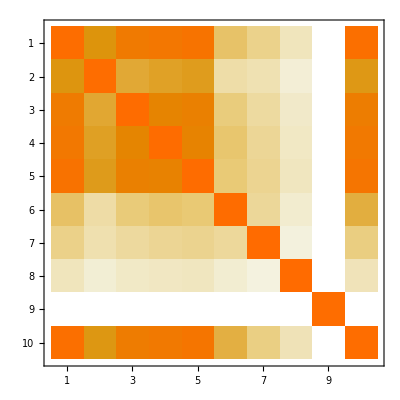

```mathematica
MatrixPlot[correlationmatrix10pL]
```

## MuC (9 parameter fit; without Br_inv)

```mathematica
Clear[chisquaremuc10p]
```

```mathematica
higgsobsmuc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,ktotal_]:={kmu^2 kmu^2/ktotal,kmu^2 ktau^2/ktotal,kmu^2 kgamma^2/ktotal,kmu^2 kw^2/ktotal,kmu^2 kz^2/ktotal,kmu^2 kg^2/ktotal,kmu^2 kt^2/ktotal,kmu^2 kb^2/ktotal,ktotal};
chisquaremuc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)^2/higgspremuc[[i]]^2)/lumif,{i,1,Length[higgspremuc]}]
```

```mathematica
140/4200//N
```

0.0333333

```mathematica
higgspremuc={2000,17.75,374,1.62, 4.49,12.8,25.23,1.72,140/4200*100}/100.
```

{20.,0.1775,3.74,0.0162,0.0449,0.128,0.2523,0.0172,0.0333333}

```mathematica
func=chisquaremuc10p[{kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal},1]
```

3380.21 (-1+(kb^2 kmu^2)/ktotal)^2+61.0352 (-1+(kg^2 kmu^2)/ktotal)^2+0.0714919 (-1+(kgamma^2 kmu^2)/ktotal)^2+0.0025 (-1+kmu^4/ktotal)^2+15.7096 (-1+(kmu^2 kt^2)/ktotal)^2+31.7397 (-1+(kmu^2 ktau^2)/ktotal)^2+900. (-1+ktotal)^2+3810.39 (-1+(kmu^2 kw^2)/ktotal)^2+496.029 (-1+(kmu^2 kz^2)/ktotal)^2

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,9}];
dlistm=Table[-RandomReal[]/20,{i,1,9}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal};
muc10p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc10p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,9},{lumif,{1}}],Method->"FinestGrained"];
muc10p//MatrixForm
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0 ∞ encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {kb,kg,kgamma,kmu,kt,ktau,ktotal,kw,kz} = {1.28603,1.81566,1.89973,1.05543,0.750831,1.57826,1.2858,1.67458,1.45048}.

((ComplexInfinity
-1.494)
(1.23786
-0.543743)
(-3.1246
-0.522061)
(1.02274
ComplexInfinity)
(1.17013
-0.530462)
(ComplexInfinity
-1.49082)
(3.3514
-5.3498)
(1.14244
-0.508855)
(0.0333333
-0.0333333))

```mathematica
higgsobsLHCratios[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={kg^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kgamma/kz,kw/kz,kb/kz,ktau/kz,kg/kz,kt/kg,ktau/kz};
higgspreLHCratiosL={2.0/100,1.8/100,2.1/100,7.4/100,7.8/100,4.5/100,5.0/100,6.1/100};
```

```mathematica
inverseinputcorrelationslhc7s2=Inverse[inputcorrelationslhc7s2/100];
chisquaremuc10pLHC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,9}];
dlistm=Table[-RandomReal[]/20,{i,1,9}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal};
muc10pLHC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc10pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc10pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,9},{lumif,{1,1/4}}],Method->"FinestGrained"];
muc10pLHC//MatrixForm
```

((0.0177923
-0.0175573) | (0.0137019
-0.0135652)
(0.0318755
-0.031914) | (0.0293305
-0.0294419)
(0.0186325
-0.0186204) | (0.0165592
-0.0165635)
(0.0138161
-0.0137379) | (0.012502
-0.0124162)
(0.0156416
-0.0156258) | (0.0149357
-0.0149235)
(0.0142081
-0.014176) | (0.0128893
-0.012834)
(0.016465
-0.0164463) | (0.0159488
-0.0159286)
(0.0201805
-0.0200303) | (0.0146738
-0.0144756)
(0.0319365
-0.031882) | (0.0164683
-0.0164644))

```mathematica
chisquaremuc10pLHCCEPC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,kmu][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]+Sum[((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu,0, ktotal][[i]]-1)/higgsprecepc[[i]])((higgsobscepc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, 0, ktotal][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/1,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,9}];
dlistm=Table[-RandomReal[]/20,{i,1,9}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma,kmu,ktotal};
muc10pLHCCEPC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc10pLHCCEPC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc10pLHCCEPC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,9},{lumif,{1,1/4}}],Method->"FinestGrained"];
muc10pLHCCEPC//MatrixForm
```

((0.00708391
-0.00706976) | (0.0052523
-0.00524656)
(0.0158339
-0.015894) | (0.0148703
-0.0149681)
(0.00919662
-0.00916536) | (0.00781082
-0.00779738)
(0.00742719
-0.00742042) | (0.00570148
-0.00569147)
(0.00816648
-0.00813919) | (0.00656823
-0.00655269)
(0.00239041
-0.00239591) | (0.00227732
-0.00228197)
(0.0128212
-0.0128269) | (0.012459
-0.0124701)
(0.00640165
-0.00641112) | (0.00392523
-0.00392259)
(0.0158493
-0.0156869) | (0.0117016
-0.0116363))

## MuC (7 parameter fit)

```mathematica
higgsobsmuc10p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_,kmu_,ktotal_]:={kmu^2 kmu^2/ktotal,kmu^2 ktau^2/ktotal,kmu^2 kgamma^2/ktotal,kmu^2 kw^2/ktotal,kmu^2 kz^2/ktotal,kmu^2 kg^2/ktotal,kmu^2 kt^2/ktotal,kmu^2 kb^2/ktotal,ktotal};
chisquaremuc10p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_,kmu_,ktotal_},lumif_]:=Sum[((higgsobsmuc10p[kz,kw,kg,kgamma,kb,kt,ktau, kmu, ktotal][[i]]-1)^2/higgspremuc[[i]]^2)/lumif,{i,1,Length[higgspremuc]}]
```

```mathematica
kh[kz,kw,kg,kgamma,kb,kt,ktau]
```

0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2

```mathematica
higgsobsmuc7p[kz_,kw_,kg_,kgamma_,kb_,kt_,ktau_]:={ktau^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 ktau^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kgamma^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kw^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kz^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kg^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kt^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],ktau^2 kb^2/kh[kz,kw,kg,kgamma,kb,kt,ktau],kh[kz,kw,kg,kgamma,kb,kt,ktau]};
chisquaremuc7p[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]
```

```mathematica
higgspremuc={2000,17.75,374,1.62, 4.49,12.8,25.23,1.72,140/4200*100}/100.
```

{20.,0.1775,3.74,0.0162,0.0449,0.128,0.2523,0.0172,0.0333333}

```mathematica
func=chisquaremuc7p[{kb,kt,kg,kw,ktau,kz,kgamma},1]
```

900. (-0.999761+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2)^2+3380.21 (-1+(kb^2 ktau^2)/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2+61.0352 (-1+(kg^2 ktau^2)/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2+0.0714919 (-1+(kgamma^2 ktau^2)/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2+15.7096 (-1+(kt^2 ktau^2)/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2+31.7422 (-1+ktau^4/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2+3810.39 (-1+(ktau^2 kw^2)/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2+496.029 (-1+(ktau^2 kz^2)/(0.000239+0.57844 kb^2+0.0856 kg^2+0.0023 kgamma^2+0.0268 kt^2+0.063921 ktau^2+0.216 kw^2+0.0267 kz^2))^2

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7p=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]],ktau>0];{chisquaremuc7p[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,ktotal}][[1]];Abs[chi2-1]≥ 0.01,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1}}],Method->"FinestGrained"];
muc7p//MatrixForm
```

((0.0195567
-0.0196469)
(0.116817
-0.132561)
(0.0593562
-0.0629004)
(0.0209058
-0.0207796)
(0.0104615
-0.0103298)
(0.029587
-0.0295767)
(1.1655
-3.1613))

```mathematica
chisquaremuc7pLHC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7pLHC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc7pLHC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1,1/4}}],Method->"FinestGrained"];
muc7pLHC//MatrixForm
```

((0.0135036
-0.0134891) | (0.00803869
-0.00804528)
(0.0314309
-0.0314877) | (0.028459
-0.0286239)
(0.0177546
-0.0177696) | (0.0153289
-0.015381)
(0.0109435
-0.0109349) | (0.00782724
-0.00782126)
(0.00604328
-0.00606069) | (0.00359285
-0.00359183)
(0.0127506
-0.0127496) | (0.0100857
-0.0100812)
(0.0141243
-0.0141232) | (0.0134633
-0.0134618))

```mathematica
chisquaremuc7pLHCCEPC[{kb_,kt_,kg_,kw_,ktau_,kz_,kgamma_},lumif_]:=Sum[((higgsobsmuc7p[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgspremuc[[i]])^2/lumif,{i,1,Length[higgspremuc]}]+Sum[((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[i]]-1)/higgsprelhc7s2[[i]])((higgsobslhc7s2[kz,kw,kg,kgamma,kb,kt,ktau,ktau][[j]]-1)/higgsprelhc7s2[[j]])inverseinputcorrelationslhc7s2[[i,j]]/1,{i,1,Length[higgsprelhc7s2]},{j,1,Length[higgsprelhc7s2]}]+Sum[((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[i]]-1)/higgsprecepc[[i]])((higgsobscepc[kz,kw,kg,kgamma,kb,kt,ktau][[j]]-1)/higgsprecepc[[j]])inverseinputcorrelations[[i,j]]/1,{i,1,Length[higgsprecepc]},{j,1,Length[higgsprecepc]}]
```

```mathematica
dlistp=Table[RandomReal[]/20,{i,1,7}];
dlistm=Table[-RandomReal[]/20,{i,1,7}];
arglist={kb,kt,kg,kw,ktau,kz,kgamma};
muc7pLHCCEPC=Parallelize[Table[{tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠10,inputlist=ReplacePart[arglist,i->1+dlistp[[i]]],inputlist=ReplacePart[arglist,i->dlistp[[i]]]];{chisquaremuc7pLHCCEPC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2,ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistp[[i]]+(dlistp[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistp[[i]];dlistp[[i]]=tmparg2;chi2t=chi2];dlistp[[i]],
tmparg=0;chi2t=0;While[chi2=NMinimize[If[i≠ 10,inputlist=ReplacePart[arglist,i->1+dlistm[[i]]],inputlist=ReplacePart[arglist,i->dlistm[[i]]]];{chisquaremuc7pLHCCEPC[inputlist,lumif],kg≥ 0,kg<2,kgamma≥ 0,kgamma<2,kb≥ 0,kb<2,kt≥ 0,kt<2,ktau≥ 0,ktau<2, kz≤2, kz≥0, kw≤2, kw≥0,kmu≥ 0, kmu<2, ktotal>0, ktotal≤2},{kz,kg,kgamma,kw,kb,kt,ktau,kmu,ktotal}][[1]];Abs[chi2-1]≥ 0.0001,tmparg2=dlistm[[i]]+(dlistm[[i]]-tmparg)(1-Sqrt[chi2])/(Sqrt[chi2]-Sqrt[chi2t]);tmparg=dlistm[[i]];dlistm[[i]]=tmparg2;chi2t=chi2];dlistm[[i]]},{i,1,7},{lumif,{1,1/4}}],Method->"FinestGrained"];
muc7pLHCCEPC//MatrixForm
```

((0.00500237
-0.00499556) | (0.003707
-0.00369634)
(0.0151885
-0.0152921) | (0.0145079
-0.0146314)
(0.0078575
-0.00784547) | (0.00698065
-0.00698145)
(0.00575565
-0.00575275) | (0.00439909
-0.00438968)
(0.00487536
-0.00488288) | (0.00291608
-0.00291936)
(0.00116055
-0.00116139) | (0.00112489
-0.00112567)
(0.0123113
-0.0123238) | (0.0121043
-0.0121197))